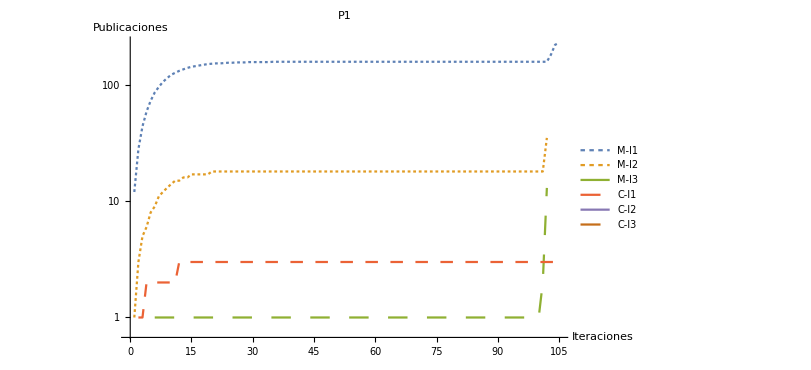
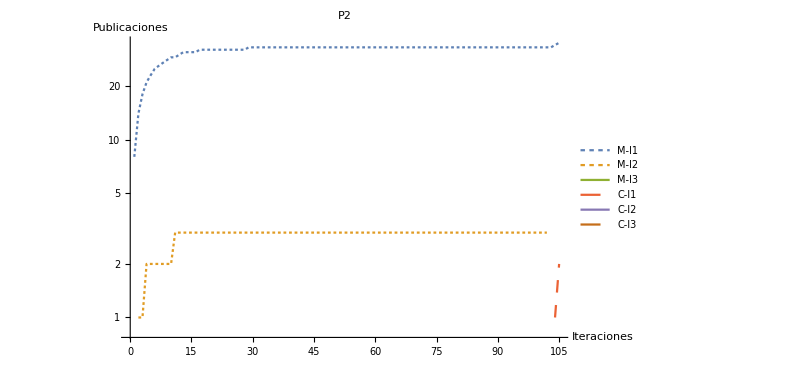
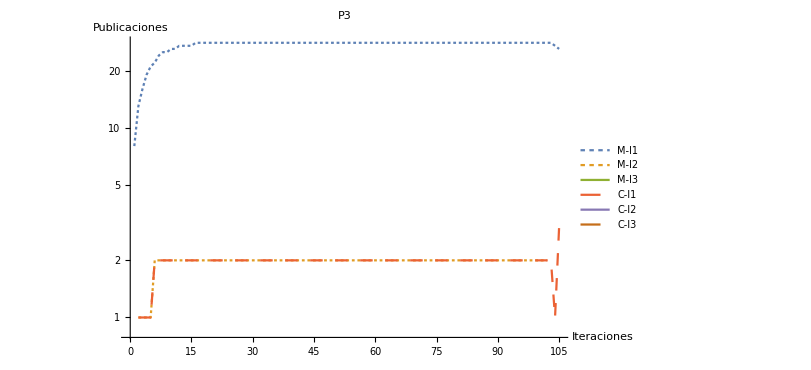
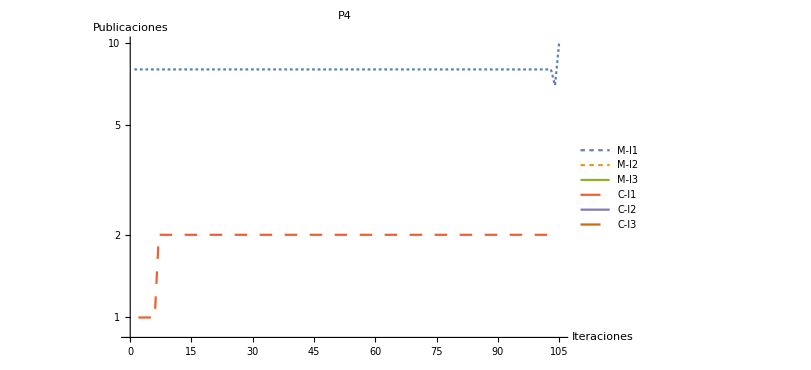
-Graphics- | -Graphics-
-Graphics- | -Graphics-

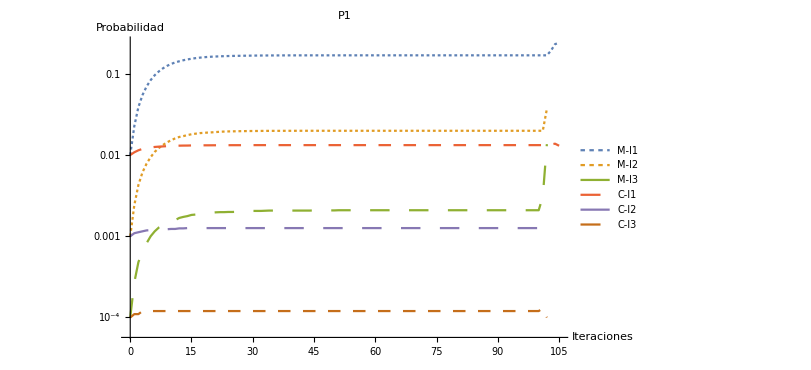
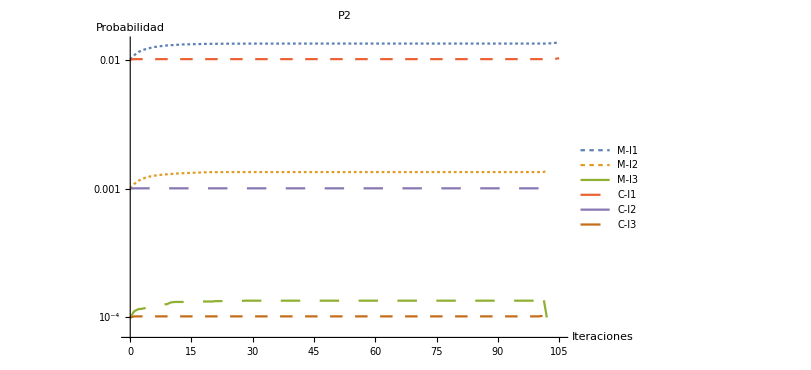
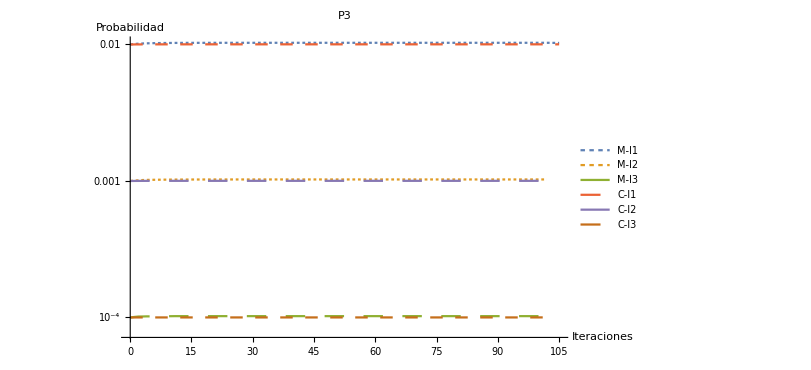
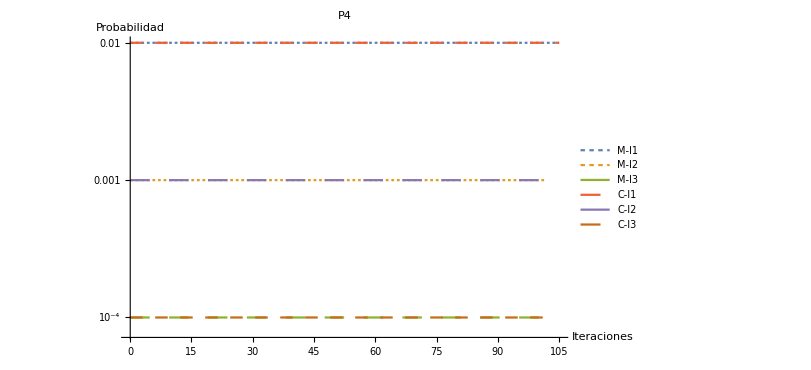
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/ConCompetencia";
SetDirectory["/home/fabianact/ActualTesis/Tesis/ModelosPresentados/Curvas/ConCompetencia100/"];
SetOptions[ListLogPlot,BaseStyle->{FontSize->18}];
pub1= Import[y<>"/averageResults/pub1-0.01-100-false-curve.csv"];
pub2= Import[y<>"/averageResults/pub1-0.001-100-false-curve.csv"];
pub3= Import[y<>"/averageResults/pub1-1.0E-4-100-false-curve.csv"];
pub4 = Import[y<>"/averageResults/pub5-0.01-100-false-curve.csv"];
pub5 = Import[y<>"/averageResults/pub5-0.001-100-false-curve.csv"];
pub6 = Import[y<>"/averageResults/pub5-1.0E-4-100-false-curve.csv"];
plotPub1 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Iteraciones","Publicaciones"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P1",PlotStyle->{Dashing[Tiny],Dashing[Tiny], Dashing[Large], Dashing[Medium], Dashing[Large], Dashing[Medium]}]];

Export["pub-1-false.png",plotPub];

pub1= Import[y<>"/averageResults/pub2-0.01-100-false-curve.csv"];
pub2= Import[y<>"/averageResults/pub2-0.001-100-false-curve.csv"];
pub3= Import[y<>"/averageResults/pub2-1.0E-4-100-false-curve.csv"];
pub4 = Import[y<>"/averageResults/pub6-0.01-100-false-curve.csv"];
pub5 = Import[y<>"/averageResults/pub6-0.001-100-false-curve.csv"];
pub6 = Import[y<>"/averageResults/pub6-1.0E-4-100-false-curve.csv"];
plotPub2 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Iteraciones","Publicaciones"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P2",PlotStyle->{Dashing[Tiny],Dashing[Tiny], Dashing[Large], Dashing[Medium], Dashing[Large], Dashing[Medium]}]];
Export["pub-2-false.png",plotPub];

pub1= Import[y<>"/averageResults/pub3-0.01-100-false-curve.csv"];
pub2= Import[y<>"/averageResults/pub3-0.001-100-false-curve.csv"];
pub3= Import[y<>"/averageResults/pub3-1.0E-4-100-false-curve.csv"];
pub4 = Import[y<>"/averageResults/pub7-0.01-100-false-curve.csv"];
pub5 = Import[y<>"/averageResults/pub7-0.001-100-false-curve.csv"];
pub6 = Import[y<>"/averageResults/pub7-1.0E-4-100-false-curve.csv"];
plotPub3 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Iteraciones","Publicaciones"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P3",PlotStyle->{Dashing[Tiny],Dashing[Tiny], Dashing[Large], Dashing[Medium], Dashing[Large], Dashing[Medium]}]];
Export["pub-3-false.png",plotPub];

pub1= Import[y<>"/averageResults/pub4-0.01-100-false-curve.csv"];
pub2= Import[y<>"/averageResults/pub4-0.001-100-false-curve.csv"];
pub3= Import[y<>"/averageResults/pub4-1.0E-4-100-false-curve.csv"];
pub4 = Import[y<>"/averageResults/pub8-0.01-100-false-curve.csv"];
pub5 = Import[y<>"/averageResults/pub8-0.001-100-false-curve.csv"];
pub6 = Import[y<>"/averageResults/pub8-1.0E-4-100-false-curve.csv"];
plotPub4 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Iteraciones","Publicaciones"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P4",PlotStyle->{Dashing[Tiny],Dashing[Tiny], Dashing[Large], Dashing[Medium], Dashing[Large], Dashing[Medium]}]];
Export["pub-4-false.png",plotPub];

pub1= Import[y<>"/averageResults/prob1-0.01-100-false-curve.csv"];
pub2= Import[y<>"/averageResults/prob1-0.001-100-false-curve.csv"];
pub3= Import[y<>"/averageResults/prob1-1.0E-4-100-false-curve.csv"];
pub4 = Import[y<>"/averageResults/prob5-0.01-100-false-curve.csv"];
pub5 = Import[y<>"/averageResults/prob5-0.001-100-false-curve.csv"];
pub6 = Import[y<>"/averageResults/prob5-1.0E-4-100-false-curve.csv"];
plotProb1 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Iteraciones","Probabilidad"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All, PlotLabel-> "P1",PlotStyle->{Dashing[Tiny],Dashing[Tiny], Dashing[Large], Dashing[Medium], Dashing[Large], Dashing[Medium]}]];

Export["prob-1-false.png",plotPub];

pub1= Import[y<>"/averageResults/prob2-0.01-100-false-curve.csv"];
pub2= Import[y<>"/averageResults/prob2-0.001-100-false-curve.csv"];
pub3= Import[y<>"/averageResults/prob2-1.0E-4-100-false-curve.csv"];
pub4 = Import[y<>"/averageResults/prob6-0.01-100-false-curve.csv"];
pub5 = Import[y<>"/averageResults/prob6-0.001-100-false-curve.csv"];
pub6 = Import[y<>"/averageResults/prob6-1.0E-4-100-false-curve.csv"];
plotProb2 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Iteraciones","Probabilidad"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All, PlotLabel-> "P2",PlotStyle->{Dashing[Tiny],Dashing[Tiny], Dashing[Large], Dashing[Medium], Dashing[Large], Dashing[Medium]}]];
Export["prob-2-false.png",plotPub];

pub1= Import[y<>"/averageResults/prob3-0.01-100-false-curve.csv"];
pub2= Import[y<>"/averageResults/prob3-0.001-100-false-curve.csv"];
pub3= Import[y<>"/averageResults/prob3-1.0E-4-100-false-curve.csv"];
pub4 = Import[y<>"/averageResults/prob7-0.01-100-false-curve.csv"];
pub5 = Import[y<>"/averageResults/prob7-0.001-100-false-curve.csv"];
pub6 = Import[y<>"/averageResults/prob7-1.0E-4-100-false-curve.csv"];
plotProb3 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Iteraciones","Probabilidad"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P3",PlotStyle->{Dashing[Tiny],Dashing[Tiny], Dashing[Large], Dashing[Medium], Dashing[Large], Dashing[Medium]}]];
Export["prob-3-false.png",plotPub];

pub1= Import[y<>"/averageResults/prob4-0.01-100-false-curve.csv"];
pub2= Import[y<>"/averageResults/prob4-0.001-100-false-curve.csv"];
pub3= Import[y<>"/averageResults/prob4-1.0E-4-100-false-curve.csv"];
pub4 = Import[y<>"/averageResults/prob8-0.01-100-false-curve.csv"];
pub5 = Import[y<>"/averageResults/prob8-0.001-100-false-curve.csv"];
pub6 = Import[y<>"/averageResults/prob8-1.0E-4-100-false-curve.csv"];
plotProb4 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Iteraciones","Probabilidad"},Joined->True, PlotLegends->{"M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All, PlotLabel-> "P4",PlotStyle->{Dashing[Tiny],Dashing[Tiny], Dashing[Large], Dashing[Medium], Dashing[Large], Dashing[Medium]}]];
Export["prob-4-false.png",plotPub];

pubTotal=Grid[{{plotPub1,plotPub2},{plotPub3,plotPub4}}]
Export["pub-total-false.png",pubTotal];
probTotal=Grid[{{plotProb1,plotProb2},{plotProb3,plotProb4}}]
Export["prob-total.false.png",probTotal];
```